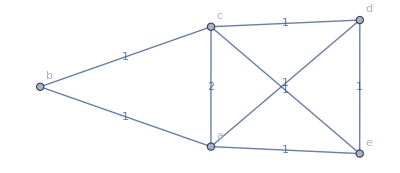

```mathematica
G=Graph[{a,b,c,d,e},{a<->b,a<->e,a<->d,a<->c,b<->c,c<->e,c<->d,d<->e},VertexLabels->Automatic,EdgeWeight->Thread[{a<->b,a<->e,a<->d,a<->c,b<->c,c<->e,c<->d,d<->e}->{1,1,1,2,1,1,1,1}],EdgeLabels->"EdgeWeight"]
```

```mathematica
MultiSet[g_?ConnectedGraphQ]:=Module[{undirectededges},Cases[EdgeList[g],_UndirectedEdge]]
```

```mathematica
Cases[{a<->e,e<->d,d<->c,c<->e,e<->b,b<->d,d<->a,a<->c,c<->b,b<->a},_UndirectedEdge]
```

{a<->e,e<->d,d<->c,c<->e,e<->b,b<->d,d<->a,a<->c,c<->b,b<->a}

```mathematica
EdgeList[G]
```

{a<->b,a<->e,a<->d,a<->c,b<->c,c<->e,c<->d,d<->e}

```mathematica
Cases[EdgeList[G],_UndirectedEdge]
```

{a<->b,a<->e,a<->d,a<->c,b<->c,c<->e,c<->d,d<->e}

```mathematica
MultiSet[G]
```

{}

```mathematica
$Version
```

13.1.0 for Microsoft Windows (64-bit) (May 24, 2022)